```mathematica
(*Check the length scale - factor of root two or root three*)
```

```mathematica
(*
Degeneracies in perfect
001:3, 011:6, 111:4
Degeneracies in Cvac for C
001:3:3(u), 011:6:3(u)|3(g), 111:4:1(u)|3(g)
Degeneracies in Cvac for Zr
001:3:1(u)|2(g), 011:6:4(g)|2(u), 111:4:4(u)
*)
```

```mathematica
kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;kjmol2evatom=1/(96.487*64);
m={12.0107,91.224,1};
ang2bohr=1/0.529177208;
ev2har=1/27.211396;
eVperAng2harperbohr=ev2har/ang2bohr;
eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
```

```mathematica
volperf={766.060875,778.68799,791.45312,808.7083508,822.6569529,846.5905360,862.257739832,885.289075,912.67299};
e0perf={-.67382051*10^3,-.67479111*10^3,-.67540188*10^3,-.67568572*10^3,-.67550095*10^3,-.67441442*10^3,-.67323280*10^3,-.67090290*10^3,-.66733277*10^3};
e0cvac={-.66257856,-.66353617,-.66414458,-.66444074,-.66427725,-.66324766,-.66211597,-.65987660,-.65643966}*10^3;
```

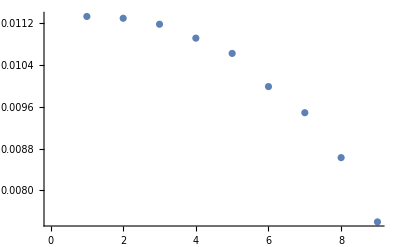

```mathematica
ListPlot[e0cvac/63-e0perf/64]
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS"];
```

```mathematica
filesC={"4.575.C.out","4.600.C.out","4.625.C.out","4.65837.C.out", "4.685.C.out","4.730.C.out","4.759.C.out","4.801.C.out","4.850.C.out"};
filesZr={"4.575.Zr.out","4.600.Zr.out","4.625.Zr.out","4.65837.Zr.out", "4.685.Zr.out","4.730.Zr.out","4.759.Zr.out","4.801.Zr.out","4.850.Zr.out"};
CdataFull=Table[ReadList[filesC[[i]],{Number,Word,Word, Number,Number,Number,Number}],{i,1,Length@filesC}];
ZrdataFull=Table[ReadList[filesZr[[i]],{Number,Word,Word, Number,Number,Number,Number}],{i,1,Length@filesZr}];

Cdata=Table[Transpose@{Transpose[CdataFull[[vol]]][[4]]/100,1000*Transpose[CdataFull[[vol]]][[7]]}//N,{vol,1,Length@filesC}];
Zrdata=Table[Transpose@{Transpose[ZrdataFull[[vol]]][[4]]/100,1000*Transpose[ZrdataFull[[vol]]][[7]]}//N,{vol,1,Length@filesZr}];

(*Types of direction*)
labelsC=Transpose[Table[Partition[CdataFull[[1]],Length@CdataFull[[1]]/5][[i]][[1]],{i,1,5}]][[3]]//TableForm
labelsZr=Transpose[Table[Partition[ZrdataFull[[1]],Length@ZrdataFull[[1]]/5][[i]][[1]],{i,1,5}]][[3]]//TableForm
```

100/x
110/xy
110/xz
111/bxyz
111/xyz

100/x
100/y
110/xz
110/yz
111/xyz

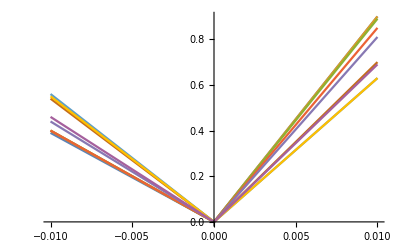

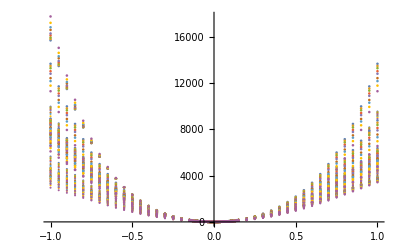

```mathematica
ListLinePlot@Table[{Zrdata[[i]][[32]],{0,0},Zrdata[[i]][[34]]},{i,1,9}]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
CdataX=Table[Partition[Cdata[[i]],65][[1]],{i,1,9}];
CdataXY=Table[Partition[Cdata[[i]],65][[2]],{i,1,9}];
CdataXZ=Table[Partition[Cdata[[i]],65][[3]],{i,1,9}];
CdataBXYZ=Table[Partition[Cdata[[i]],65][[4]],{i,1,9}];
CdataXYZ=Table[Partition[Cdata[[i]],65][[5]],{i,1,9}];
cdataAllDir={CdataX,CdataXY,CdataXZ,CdataBXYZ,CdataXYZ};
ZrdataX=Table[Partition[Zrdata[[i]],65][[1]],{i,1,9}];
ZrdataY=Table[Partition[Zrdata[[i]],65][[2]],{i,1,9}];
ZrdataXY=Table[Partition[Zrdata[[i]],65][[3]],{i,1,9}];
ZrdataYZ=Table[Partition[Zrdata[[i]],65][[4]],{i,1,9}];
ZrdataXYZ=Table[Partition[Zrdata[[i]],65][[5]],{i,1,9}];
zrdataAllDir={ZrdataX,ZrdataY,ZrdataXY,ZrdataYZ,ZrdataXYZ};
```

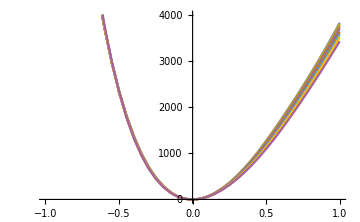
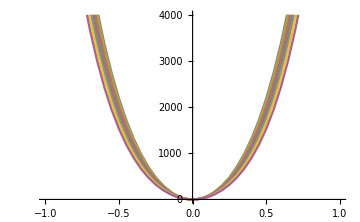
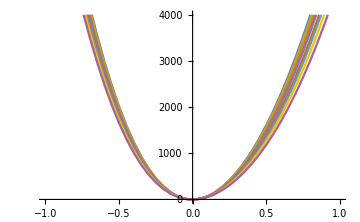
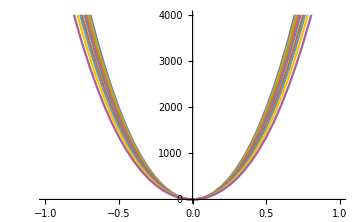
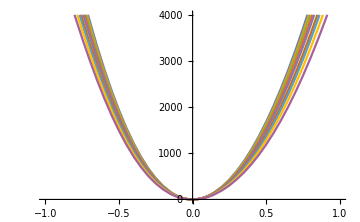

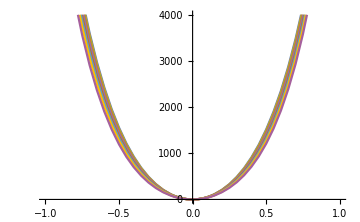
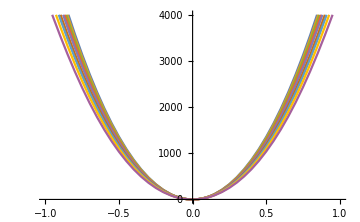
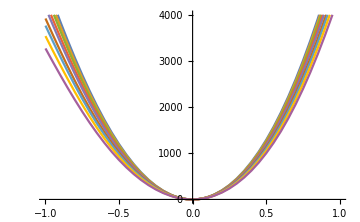

```mathematica
Table[ListLinePlot[zrdataAllDir[[i]],PlotRange->{All,{0,4000}},ImageSize->Medium],{i,1,5}]
Table[ListLinePlot[cdataAllDir[[i]],PlotRange->{All,{0,4000}},ImageSize->Medium],{i,1,5}]
```

```mathematica
V[1,2,x_]:=Table[Table[Fit[cdataAllDir[[type]][[vol]],{x^2},x],{type,1,5}],{vol,1,9}]
V[1,3,x_]:=Table[Table[Fit[cdataAllDir[[type]][[vol]],{x^2,x^3},x],{type,1,5}],{vol,1,9}]
V[1,4,x_]:=Table[Table[Fit[cdataAllDir[[type]][[vol]],{x^2,x^3,x^4},x],{type,1,5}],{vol,1,9}]
V[1,5,x_]:=Table[Table[Fit[cdataAllDir[[type]][[vol]],{x^2,x^3,x^4,x^5},x],{type,1,5}],{vol,1,9}]
V[1,6,x_]:=Table[Table[Fit[cdataAllDir[[type]][[vol]],{x^2,x^3,x^4,x^5,x^6},x],{type,1,5}],{vol,1,9}]
V[2,2,x_]:=Table[Table[Fit[zrdataAllDir[[type]][[vol]],{x^2},x],{type,1,5}],{vol,1,9}]
V[2,3,x_]:=Table[Table[Fit[zrdataAllDir[[type]][[vol]],{x^2,x^3},x],{type,1,5}],{vol,1,9}]
V[2,4,x_]:=Table[Table[Fit[zrdataAllDir[[type]][[vol]],{x^2,x^3,x^4},x],{type,1,5}],{vol,1,9}]
V[2,5,x_]:=Table[Table[Fit[zrdataAllDir[[type]][[vol]],{x^2,x^3,x^4,x^5},x],{type,1,5}],{vol,1,9}]
V[2,6,x_]:=Table[Table[Fit[zrdataAllDir[[type]][[vol]],{x^2,x^3,x^4,x^5,x^6},x],{type,1,5}],{vol,1,9}]
```

```mathematica
labelsC
```

100/x
110/xy
110/xz
111/bxyz
111/xyz

```mathematica
V[2,4,t]
```

{{6361. t^2-5608.09 t^3+3371.9 t^4,6956.35 t^2-6.31728×10^-13 t^3+6641.59 t^4,7251.12 t^2-1488.38 t^3+311.129 t^4,7740.46 t^2+1.34978×10^-13 t^3+1071.33 t^4,7371.93 t^2-777.024 t^3-279.085 t^4},{6292.71 t^2-5664.89 t^3+3486.23 t^4,6700.46 t^2+7.54124×10^-13 t^3+6706.1 t^4,7104.48 t^2-1484.27 t^3+343.024 t^4,7502.09 t^2+4.75531×10^-13 t^3+1116.94 t^4,7197.81 t^2-771.677 t^3-248.895 t^4},{6223.75 t^2-5727.05 t^3+3604.27 t^4,6446.24 t^2-6.56456×10^-13 t^3+6764.97 t^4,6958.09 t^2-1482.37 t^3+373.3 t^4,7265.22 t^2-4.07382×10^-13 t^3+1160.22 t^4,7024.33 t^2-767.559 t^3-220.252 t^4},{6129.98 t^2-5819.22 t^3+3769.28 t^4,6109.2 t^2+2.90279×10^-14 t^3+6834.35 t^4,6762.51 t^2-1483.3 t^3+411.889 t^4,6951.32 t^2-6.84752×10^-14 t^3+1214.05 t^4,6793.03 t^2-763.899 t^3-183.653 t^4},{6052.49 t^2-5900.94 t^3+3909.19 t^4,5841.16 t^2+7.1878×10^-13 t^3+6882.44 t^4,6605.2 t^2-1486.8 t^3+442.358 t^4,6702.03 t^2+9.83762×10^-14 t^3+1253.95 t^4,6617.51 t^2-763.858 t^3-165.744 t^4},{5912.02 t^2-6058.4 t^3+4169.6 t^4,5385.69 t^2+5.67981×10^-15 t^3+6950.85 t^4,6332.71 t^2-1498.45 t^3+497.403 t^4,6277.95 t^2-2.64371×10^-13 t^3+1319.08 t^4,6287.96 t^2-762.656 t^3-102.265 t^4},{5815.64 t^2-6175.14 t^3+4355.98 t^4,5089.31 t^2+1.3973×10^-12 t^3+6986.58 t^4,6152.91 t^2-1509.94 t^3+535.493 t^4,6001.03 t^2-9.79076×10^-14 t^3+1360.91 t^4,6077.79 t^2-764.782 t^3-65.8479 t^4},{5674.84 t^2-6370.95 t^3+4652.02 t^4,4659.12 t^2-8.55875×10^-15 t^3+7021.89 t^4,5892.28 t^2-1532.87 t^3+590.198 t^4,5596.83 t^2-1.09633×10^-13 t^3+1419.41 t^4,5772.08 t^2-770.999 t^3-13.0536 t^4},{5519.18 t^2-6651.12 t^3+5040.35 t^4,4159.44 t^2-1.03222×10^-14 t^3+7030.69 t^4,5595.06 t^2-1570.63 t^3+648.345 t^4,5123. t^2+5.28499×10^-14 t^3+1481.1 t^4,5418.6 t^2-783.86 t^3+44.3426 t^4}}

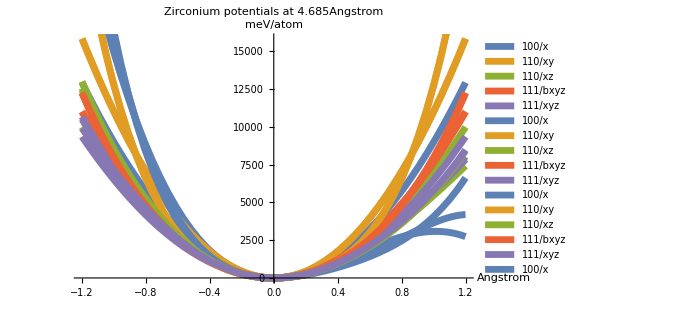

```mathematica
Show[Table[Plot[Evaluate@Table[V[2,i,x][[5]][[j]],{j,1,5}],{x,-1.2,1.2},PlotStyle->Thickness[0.01],PlotLegends->SwatchLegend[labelsC[[1]]],PlotLabel->"Zirconium potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],{i,2,5}],ImageSize->500]
```

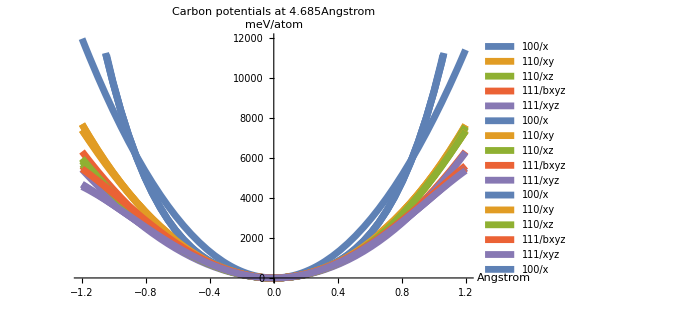

```mathematica
Show[Table[Plot[Evaluate@Table[V[1,i,x][[5]][[j]],{j,1,5}],{x,-1.2,1.2},PlotStyle->Thickness[0.01],PlotLegends->SwatchLegend[labelsC[[1]]],PlotLabel->"Carbon potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],{i,3,6}],ImageSize->500]
```

```mathematica
(*Symmetry analysis*)
labelsC
labelsZr
V[1,3,x][[5]]
V[2,3,x][[5]]
```

100/x
110/xy
110/xz
111/bxyz
111/xyz

100/x
100/y
110/xz
110/yz
111/xyz

{8119.77 x^2-161.535 x^3,5125.15 x^2-13.4945 x^3,4593.91 x^2+448.471 x^3,4393.54 x^2-3.54851×10^-13 x^3,4069.9 x^2+245.942 x^3}

{8978.99 x^2-5900.94 x^3,10993.5 x^2-8.09518×10^-14 x^3,6936.35 x^2-1486.8 x^3,7640.76 x^2-6.15912×10^-15 x^3,6493.43 x^2-763.858 x^3}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=40;
(*Define bounds for plotting and solving eigenproblem*)
B=1.1;H=2000;
power={2,3,4,5,6};
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x]/.i->power[[j]],{j,1,5,1}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x]/.i->power[[j]],{j,1,5,1}];
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

```mathematica
cAnh=Table[Table[Table[NDEigensystem[ℒallc[[power]][[vol]][[dir]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{dir,1,5}],{vol,1,9}],{power,1,5}];
```

```mathematica
zrAnh=Table[Table[Table[NDEigensystem[ℒallz[[power]][[vol]][[dir]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{dir,1,5}],{vol,1,9}],{power,1,5}];
```

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Mathematica_Files"]
DumpSave["dump.CVAC.cAnh.mx",cAnh]
DumpSave["dump.CVAC.zrAnh.mx",zrAnh]
```

/Volumes/MicroSD/2_PostDoc_SD/Mathematica_Files

{{{1},3,{{1},7,{{{12.4661,37.4656,62.5995,87.8661,32,988.888,1018.05,1047.31,1076.68},{1}},3,{{1},1}}}}}
 |  |  |  |

{{{1},3,{{1},7,{1,3,{{5.30689,15.9214,26.5378,37.156,32,388.601,399.282,409.965,420.65},{1}}}}}}
 |  |  |  |

```mathematica
(*cAnh[[power_]][[vol_]][[dir]][[val|vec]]*)
```

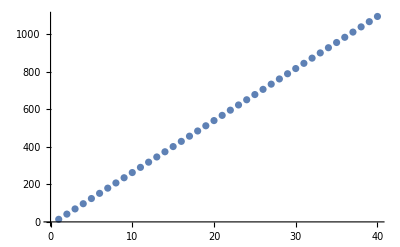

```mathematica
ListPlot@cAnh[[4]][[4]][[3]][[1]][[1;;40]]
```

```mathematica
Table[Table[cAnh[[power]][[4]][[dir]][[1]][[1]],{dir,1,5}],{power,1,5}]//TableForm
```

18.4945 | 14.7711 | 14.0064 | 13.6916 | 13.1878
18.4944 | 14.7711 | 14.0062 | 13.6916 | 13.1877
13.6192 | 14.4703 | 13.8486 | 14.5091 | 14.0821
13.6192 | 14.4703 | 13.8487 | 14.5091 | 14.082
14.0088 | 14.2671 | 13.6697 | 14.4056 | 13.9941

```mathematica
volDirAnhC=Table[Table[(cAnh[[power]][[4]][[dir]][[1]][[1;;40]]/(2*cAnh[[power]][[4]][[dir]][[1]][[1]]))/(Table[0.5+i,{i,0,39}]),{dir,1,5}],{power,1,5}];
volDirAnhZr=Table[Table[(zrAnh[[power]][[4]][[dir]][[1]][[1;;40]]/(2*zrAnh[[power]][[4]][[dir]][[1]][[1]]))/(Table[0.5+i,{i,0,39}]),{dir,1,5}],{power,1,5}];
```

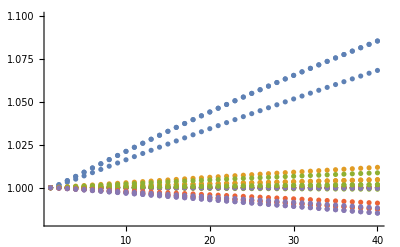

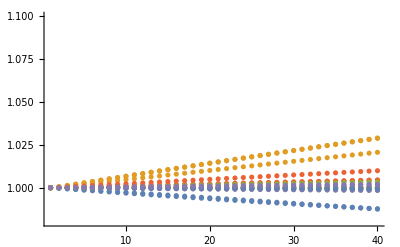

```mathematica
Show[Table[ListPlot[volDirAnhC[[i]]],{i,1,5}],PlotRange->{All,{0.98,1.1}}]
Show[Table[ListPlot[volDirAnhZr[[i]]],{i,1,5}],PlotRange->{All,{0.98,1.1}}]
```

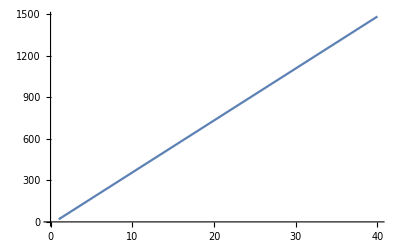

```mathematica
Show@Table[Table[ListLinePlot@cAnh[[j]][[1]][[i]][[1]],{i,1,1}],{j,1,1}]
```

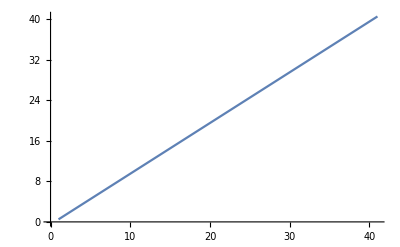

```mathematica
ListLinePlot@Table[i+0.5,{i,0,40}]
```

```mathematica
cAnh[[1]][[1]][[1]][[1]]/(2cAnh[[1]][[1]][[1]][[1]][[1]])
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5}

```mathematica
fr[T_,spectrumZ_,spectrumC_,maxEigen_,xFactor_,pFactor_]:=-K2meV*(pFactor)*T*Log[{Total[Exp[-xFactor*spectrumZ/(K2meV*T)]],Total[Exp[-xFactor*spectrumC/(K2meV*T)]]}]
```

```mathematica
(*cAnh[[power_]][[vol_]][[dir]][[val|vec]]*)
```

```mathematica
cAnhSpec=cAnh[[4]][[4]][[3]][[1]][[1;;40]]
zrAnhSpec=zrAnh[[4]][[4]][[3]][[1]][[1;;40]]
```

{13.8487,41.5472,69.2485,96.9524,124.659,152.368,180.08,207.795,235.512,263.232,290.955,318.68,346.408,374.138,401.872,429.607,457.346,485.087,512.831,540.577,568.326,596.077,623.831,651.588,679.347,707.109,734.873,762.641,790.41,818.182,845.957,873.734,901.514,929.296,957.081,984.869,1012.66,1040.45,1068.25,1096.04}

{6.0881,18.2638,30.4389,42.6134,54.7873,66.9606,79.1334,91.3056,103.477,115.648,127.819,139.989,152.159,164.328,176.496,188.664,200.831,212.998,225.165,237.331,249.496,261.661,273.826,285.99,298.153,310.317,322.479,334.642,346.803,358.965,371.126,383.286,395.447,407.606,419.766,431.925,444.083,456.241,468.399,480.557}

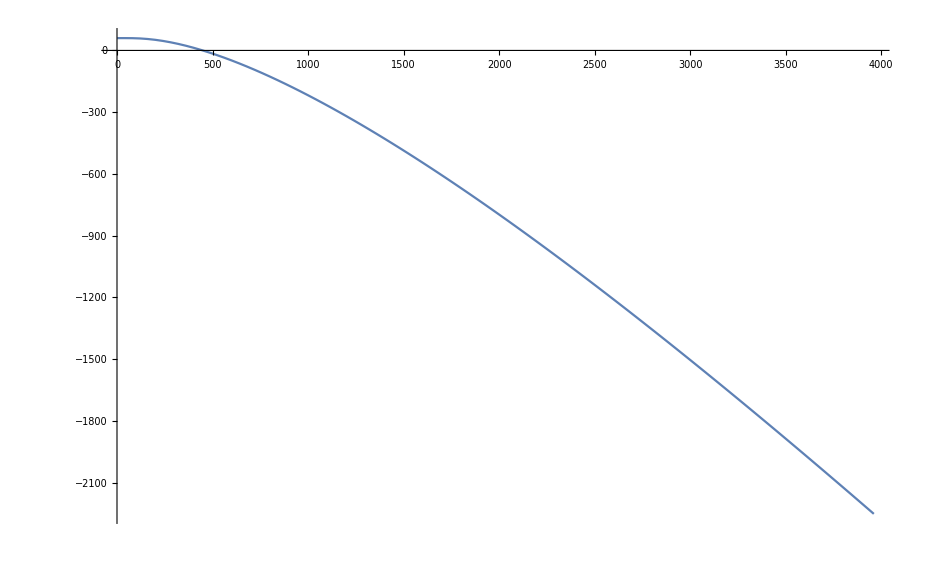

```mathematica
gibbs=Table[{t,Total@fr[t,cAnhSpec,zrAnhSpec,40,2,1.5]},{t,1,4000,40}];
ListLinePlot@gibbs
```

```mathematica
vols={"4.575Å","4.600Å","4.625Å","4.658Å","4.685Å","4.730Å","4.759Å","4.801Å","4.850Å"};
maxT=4000;minT=300;dT=100;
plab=Flatten@Table[StringJoin[vols[[i]],labelsC[[1]][[j]]],{j,1,3},{i,1,9}]
```

{4.575Å100/x,4.600Å100/x,4.625Å100/x,4.658Å100/x,4.685Å100/x,4.730Å100/x,4.759Å100/x,4.801Å100/x,4.850Å100/x,4.575Å110/xy,4.600Å110/xy,4.625Å110/xy,4.658Å110/xy,4.685Å110/xy,4.730Å110/xy,4.759Å110/xy,4.801Å110/xy,4.850Å110/xy,4.575Å110/xz,4.600Å110/xz,4.625Å110/xz,4.658Å110/xz,4.685Å110/xz,4.730Å110/xz,4.759Å110/xz,4.801Å110/xz,4.850Å110/xz}

```mathematica
ListPlot3D@T
```

```mathematica
ListPlot3D[Partition[Flatten@Table[Table[{q,t,Total@fr[t,q*cHarSpec,q*zrHarSpec,40,2,1.5]-Total@fr[t,cHarSpec,zrHarSpec,40,2,1.5]},{t,1,4000,50}],{q,0.7,1.5,0.01}],3],AxesLabel->{"α","T (K)","Fah (meV/atom)"},ImageSize->Large]
```

-Graphics3D-

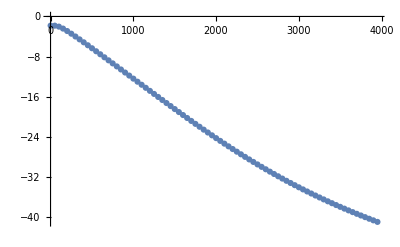

```mathematica
ListPlot@Table[{t,Total@fr[t,cAnhSpec,zrAnhSpec,40,2,1.5]-Total@fr[t,cHarSpec,zrHarSpec,40,2,1.5]},{t,1,4000,50}]
```

```mathematica
ListPlot3D@Partition[Flatten@Table[Table[{q,t,Total@fr[t,q*cAnhSpec,q*zrAnhSpec,40,2,1.5]-Total@fr[t,cHarSpec,zrHarSpec,40,2,1.5]},{t,1,4000,50}],{q,0.95,1.2,0.01}],3]
```

-Graphics3D-

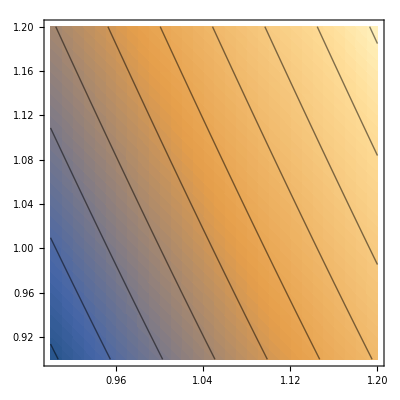

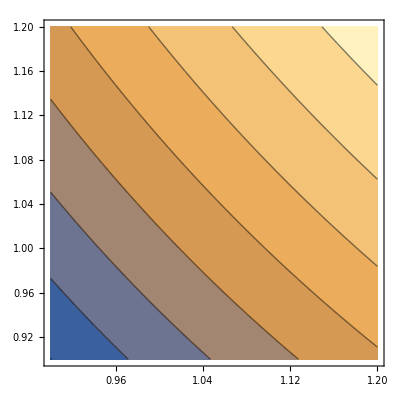

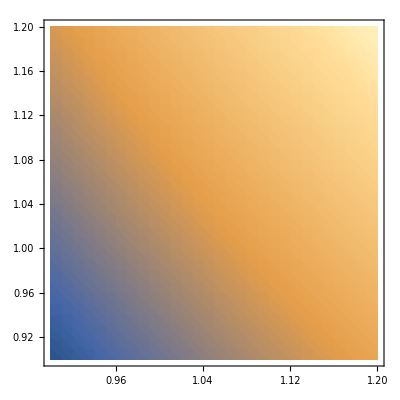

```mathematica
Show[{ListDensityPlot[Partition[Flatten@With[{t=100},Table[Table[{p,q,Total@fr[t,p*cAnhSpec,q*zrAnhSpec,40,2,1.5]-Total@fr[t,cHarSpec,zrHarSpec,40,2,1.5]},{p,0.9,1.2,0.01}],{q,0.9,1.2,0.01}]],3]],ListContourPlot[Partition[Flatten@With[{t=100},Table[Table[{p,q,Total@fr[t,p*cAnhSpec,q*zrAnhSpec,40,2,1.5]-Total@fr[t,cHarSpec,zrHarSpec,40,2,1.5]},{p,0.9,1.2,0.01}],{q,0.9,1.2,0.01}]],3],ContourStyle->Opacity[0.5],ContourShading->Opacity[0.15]]}]
ListContourPlot@Partition[Flatten@With[{t=1000},Table[Table[{p,q,Total@fr[t,p*cAnhSpec,q*zrAnhSpec,40,2,1.5]-Total@fr[t,cHarSpec,zrHarSpec,40,2,1.5]},{p,0.9,1.2,0.01}],{q,0.9,1.2,0.01}]],3]
ListDensityPlot@Partition[Flatten@With[{t=4000},Table[Table[{p,q,Total@fr[t,p*cAnhSpec,q*zrAnhSpec,40,2,1.5]-Total@fr[t,cHarSpec,zrHarSpec,40,2,1.5]},{p,0.9,1.2,0.01}],{q,0.9,1.2,0.01}]],3]
```

```mathematica
ListPlot3D@Partition[Flatten@With[{t=4000},Table[Table[{p,q,Total@fr[t,p*cAnhSpec,q*zrAnhSpec,40,2,1.5]-Total@fr[t,cHarSpec,zrHarSpec,40,2,1.5]},{p,0.9,1.2,0.01}],{q,0.9,1.2,0.01}]],3]
```

-Graphics3D-

825.605-4.80319 x+0.00499226 x^2-1.66741×10^-6 x^3

20668.6-12550.6 x+2437.61 x^2-156.062 x^3

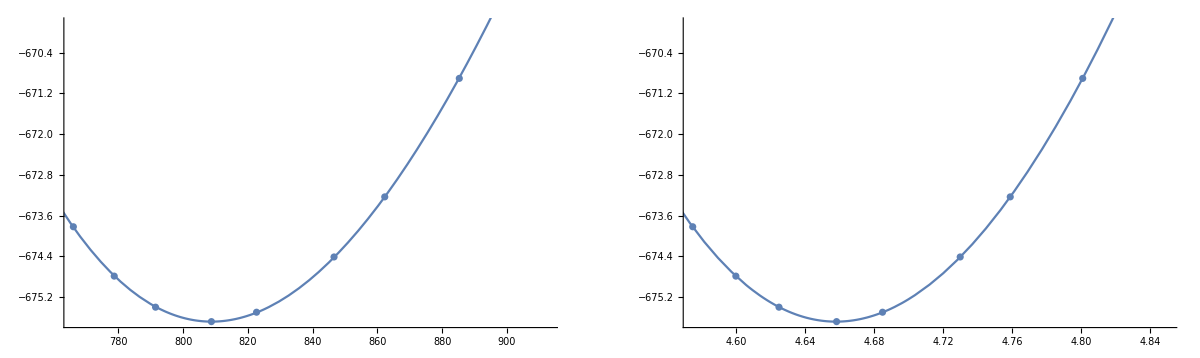

```mathematica
e0volfit=Fit[Transpose[{volperf,e0perf}],{1,x,x*x,x*x*x},x];
e0afit=Fit[Transpose[{0.5(volperf^(1/3)),e0perf}],{1,x,x*x,x*x*x},x];
e0volfit
e0afit
GraphicsGrid[{{Show[ListPlot[Transpose[{volperf,e0perf}]],Plot[e0volfit,{x,750,900}]],Show[ListPlot[Transpose[{0.5(volperf^(1/3)),e0perf}]],Plot[e0afit,{x,4.5,4.9}]]}},ImageSize->1200]
```

799.714-4.6841 x+0.00486948 x^2-1.62746×10^-6 x^3

20185.4-12264.3 x+2383.16 x^2-152.677 x^3

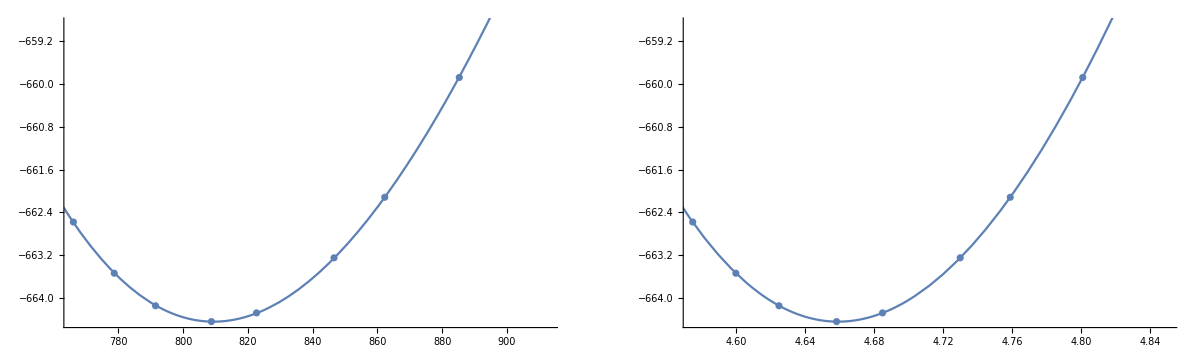

```mathematica
e0volfitcvac=Fit[Transpose[{volperf,e0cvac}],{1,x,x*x,x*x*x},x];
e0afitcvac=Fit[Transpose[{0.5(volperf^(1/3)),e0cvac}],{1,x,x*x,x*x*x},x];
e0volfitcvac
e0afitcvac
GraphicsGrid[{{Show[ListPlot[Transpose[{volperf,e0cvac}]],Plot[e0volfitcvac,{x,750,900}]],Show[ListPlot[Transpose[{0.5(volperf^(1/3)),e0cvac}]],Plot[e0afitcvac,{x,4.5,4.9}]]}},ImageSize->1200]
```

20668.6-12550.6 x+2437.61 x^2-156.062 x^3

-675.686

{1.86551,0.894914,0.284144,0.000304377,0.185074,1.2716,2.45322,4.78312,8.35325}

{4.575,4.6,4.625,4.65837,4.685,4.73,4.759,4.801,4.85}

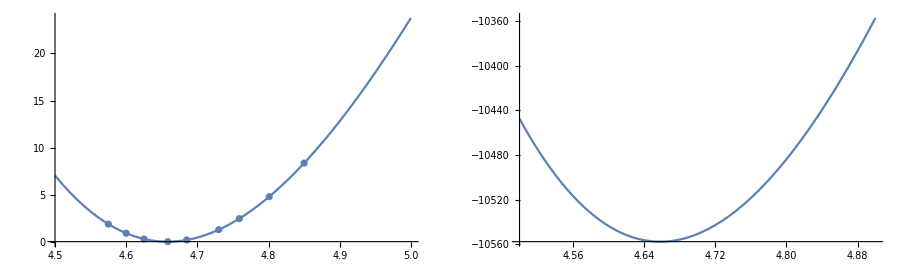

```mathematica
e0afit
eafitMin=FindMinimum[Evaluate@e0afit,x][[1]]
e0=e0perf[[1;;9]]-eafitMin
a0=0.5(volperf^(1/3))
GraphicsGrid[{{Show[Plot[Evaluate@Fit[Transpose[{a0,e0}],{1,x,x*x,x*x*x},x],{x,4.5,5}],ListPlot[Transpose[{a0,e0}]]],Plot[e0afit*1000/64,{x,4.5,4.9}]}},ImageSize->900]
```

20185.4-12264.3 x+2383.16 x^2-152.677 x^3

-664.441

{1.86265,0.905041,0.296631,0.000470526,0.163961,1.19355,2.32524,4.56461,8.00155}

{4.575,4.6,4.625,4.65837,4.685,4.73,4.759,4.801,4.85}

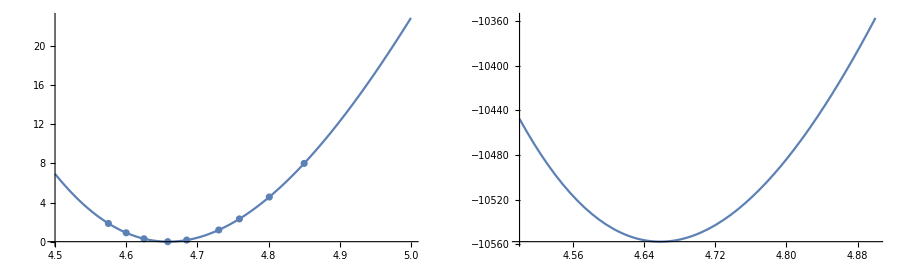

```mathematica
e0afitcvac
eafitMincvac=FindMinimum[Evaluate@e0afitcvac,x][[1]]
e0c=e0cvac[[1;;9]]-eafitMincvac
a0=0.5(volperf^(1/3))
GraphicsGrid[{{Show[Plot[Evaluate@Fit[Transpose[{a0,e0c}],{1,x,x*x,x*x*x},x],{x,4.5,5}],ListPlot[Transpose[{a0,e0c}]]],Plot[e0afit*1000/64,{x,4.5,4.9}]}},ImageSize->900]
```

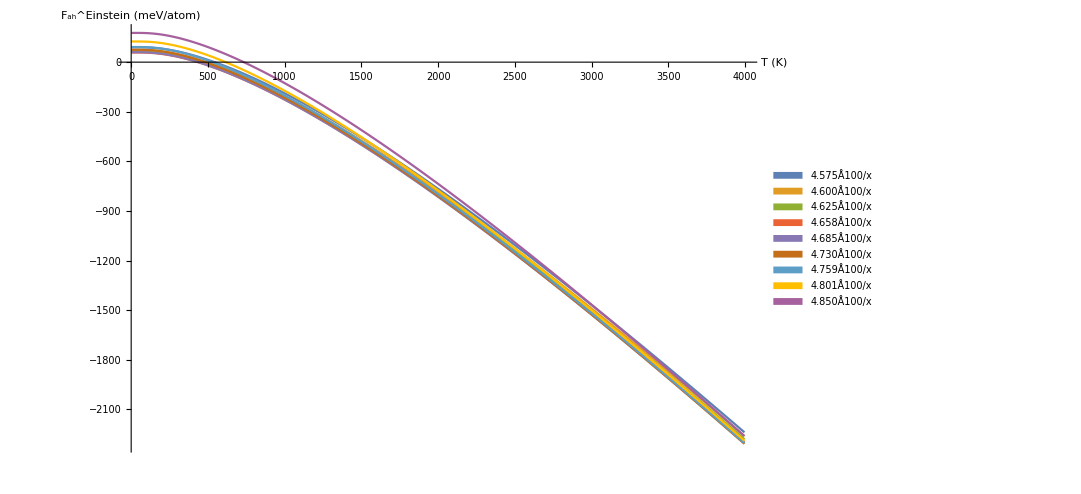

```mathematica
ListLinePlot[Table[Table[{t,1000/64*e0c[[vol]]+Total@fr[t,cAnh[[3]][[vol]][[1]][[1]],zrAnh[[3]][[vol]][[1]][[1]],40,2,1.5]},{t,1,4000,5}],{vol,1,9}],PlotLegends->SwatchLegend[plab],ImageSize->800,AxesLabel->{"T (K)","F_ah^Einstein (meV/atom)"},PlotStyle->PointSize[0.2]]
```

332178.-195853. x+38155.3 x^2-2453.58 x^3

{-664.441,{x→4.65928}}

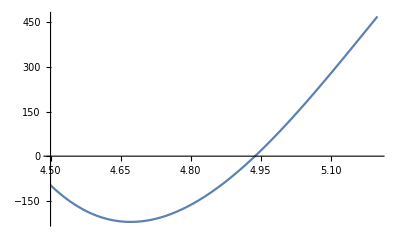

{-220.927,{x→4.67157}}

-Graphics-

```mathematica
fitcvac=Fit[Table[{a0[[vol]],1000/63*e0c[[vol]]+Total@fr[t,cAnh[[5]][[vol]][[1]][[1]],zrAnh[[5]][[vol]][[1]][[1]],40,2,1.5]},{vol,1,9}]/.t->1000,{1,x,x*x,x*x*x},x]
Minimize[e0afitcvac,x]
Plot[fitcvac,{x,4.5,5.2}]
Minimize[{fitcvac,4.5<x<4.9},x]
Plot[fitcvac,{x,4.5,5.2}]
```